Corso di Laboratorio Computazionale — Corso di Laurea in Matematica — Università di Padova.

Anno Accademico 2019-2020

# Esercizi 1. Grafica e teoria dei numeri

Notebook del gruppo Cammelli Tonanti.
Componenti del gruppo: Francesco Tognetti, Riccardo Cazzin.
Se ci sono stati collaborazioni o aiuti al di fuori del gruppo, dichiararli.
In collaborazione con
Aiutati da

## Esercizio 1.3 (Teorema dei numeri primi).

### Testo dell’esercizio

Il teorema dei numeri primi afferma che le funzioni π(n), n/(log(n)), li(n) sono asintotiche per n→∞. Investigare numericamente quest’affermazione.

### Svolgimento

Ricorrendo al risolutore di limiti interno a Mathematica, possiamo intravedere l’asintoticità per n→∞.

```mathematica
{
Limit[PrimePi[n]/(n/Log[n]),n->∞],
Limit[PrimePi[n]/LogIntegral[n],n->∞]
}
```

Occorre precisare che ciò non significa che il modulo della differenza tra due delle funzioni in esame sia infinitesimo. Come si vede nel grafico seguente, la differenza in valore assoluto tra π(n) e n/(log(n)) è tendenzialmente crescente. Dal grafico, però, non è chiaro quale α>0 sia tale che n^α sia asintotico a |π(n)-n/(log(n))| — né, in realtà, sono presenti elementi che assicurino l’esistenza di un tale α.

```mathematica
Manipulate[
LogLogPlot[
{
Abs[PrimePi[x]-x/Log[x]],
x^α
},
{x,10^k,10^(k+3)},
PlotStyle->{Red,Black},
PlotLegends->{TraditionalForm[Abs[PrimePi[x]-x/Log[x]]],TraditionalForm[x^α]},Ticks->{N@(10^Range[k,k+3]),Automatic}(*La N impedisce che i numeri sotto i tick compaiano per esteso anche quando troppo lunghi.*)
],
{k,Range[9]},(*Questa sintassi permette di ottenere un controllo a tendina anziché a slider.*)
{α,0.1,1}
]
```

Confrontando π(n) con li(n), seppur con oscillazioni più pronunciate, si ottiene ugualmente che la differenza in valore assoluto tra le due funzioni non è infinitesima, ma tendente a ∞ per n→∞. Anche in questo caso non è facile individuare “ad occhio” l’esponente β>0, se esiste, tale che n^β sia asintotico a |π(n)-li(n)|.

```mathematica
Manipulate[
LogLogPlot[
{
Abs[PrimePi[x]-LogIntegral[x]],
x^β
},
{x,10^k,10^(k+2)},
PlotStyle->{Red,Black},
PlotLegends->{TraditionalForm[Abs[PrimePi[x]-LogIntegral[x]]],TraditionalForm[x^β]},Ticks->{N@(10^Range[k,k+2]),Automatic}
],
{k,Range[10]},
{β,0.3,.45}
]
```

Il grafico seguente indaga “visivamente” l’asintoticità di π(n) e n/(log(n)), ovvero mostra se il rapporto tra le due funzioni tende a 1. Si può notare che il rapporto è definitivamente decrescente ed inferiormente limitato da 1, ma il decadimento è molto lento — piú lento di qualunque funzione n^γ+1 con γ<0: per ogni γ<0, infatti, è sufficiente considerare (anche solo guardando il grafico) un n abbastanza grande a partire dal quale n^γ+1<(π(n))/(n / log(n)).

```mathematica
Manipulate[
LogLogPlot[
PrimePi[x]/(x/Log[x]),
{x,10^k,10^(k+5)},
PlotStyle->Blue,Ticks->{N@(10^Range[k,k+5]),Automatic},PlotLegends->{TraditionalForm[Defer@(PrimePi[x]/(x/Log[x]))]},PlotRange->{.99,1.3}
],
{k,Range[0,9]}
]
```

L’asintoticità di π(n) e li(n), invece, è molto più evidente a partire dal grafico: già per n>10^5 il rapporto tra le due funzioni è “molto vicino” a 1, mentre nel caso precedente la convergenza risulta molto piú lenta

```mathematica
Manipulate[
LogLogPlot[
LogIntegral[x]/PrimePi[x],
{x,10^k,10^(k+5)},
PlotStyle->Blue,Ticks->{N@(10^Range[k,k+5]),Automatic},PlotLegends->{TraditionalForm[PrimePi[x]/LogIntegral[x]]},PlotRange->{0.999,1.5}
],
{k,Range[9]}
]
```

L’evidenza richiesta

```mathematica
Manipulate[
LogLogPlot[PrimePi[x]/(x/Log[x])-1,
{x,10^k,10^(k+3)},
PlotStyle->Blue,
Ticks->{N@(10^Range[k,k+3]),Automatic},PlotRange->{0.01,0.3}
],
{k,Range[0,9]}
]
```

```mathematica
Manipulate[
LogLogPlot[LogIntegral[x]/PrimePi[x]-1,
{x,10^k,10^(k+3)},
PlotStyle->Blue,
Ticks->{N@(10^Range[k,k+3]),Automatic}
],
{k,Range[9]}
]
```

## Esercizio 1.4 (Catenaria).

### Testo dell’esercizio

Se, nel piano xy, un cerchio di raggio r rotola senza strisciare sull’asse x, un punto P del cerchio descrive, nel piano xy, una curva chiamata catenaria, di equazioni parametriche

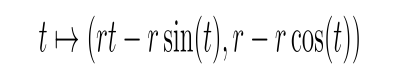

Produrre un’animazione (e magari un filmato) che mostra il cerchio (o un disco) che rotola, il punto P su di essa, e la curva descritta da P nel piano.

### Svolgimento